This is a text cell. My name is Bob Schmitz

## Section 1: Basic Computations

```mathematica
(*Step 5*)
Sin[2Pi/3]
Sqrt[80089]
ArcTan[2.4]
```

(√3)/2

283

1.17601

## Section 2: Using the Palettes

```mathematica
(*Step 7*)
Cos[81Pi/4]
∫_0^4 (x+1)^(12)ⅆx
D[((x^2+y^2)/x), x]
```

1/(√2)

1220703124/13

2-(x^2+y^2)/x^2

## Section 3: Calculus

```mathematica
(*Step 9*)
f[x_,y_]:=x^2-Sin[2y]
```

```mathematica
(*Step 10*)
fx =D[f[x,y],x]
fy:=D[f[x, y], y]
fyy=D[f[x, y], y, y]
```

2 x

4 Sin[2 y]

```mathematica
(*Step 11*)
fx/.{x->0,y->1}
fy/.{x->0,y->1}
```

0

-2 Cos[2]

```mathematica
(*Step 12*)
g[x_]:=f[x,1]
D[g[a],a]/.a->0
```

0

```mathematica
(*Step 13*)
h[y_]:=f[0,y]
D[h[b],b]/.b->1
```

-2 Cos[2]

```mathematica
-2 Cos[2]
```

-2 Cos[2]

## Section 4: Plotting

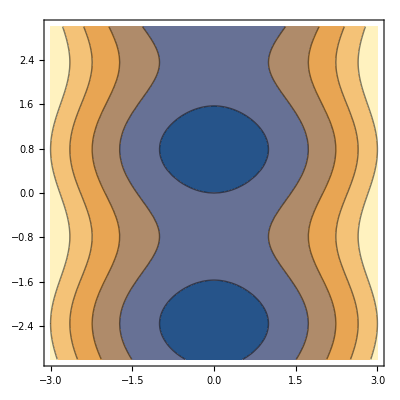

```mathematica
(*Step 15*)
ContourPlot[f[x,y], {x, -3, 3}, {y, -3, 3}]
```

```mathematica
(*Step 16*)
Clear[surface]
surface=Plot3D[f[x,y], {x, -3, 3}, {y, -3, 3}, Mesh->None, PlotStyle->Blue, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(*Step 17*)
Clear[r,s]
r[t_,y_:1]:={x=t, y, z=f[x,y]}
(*Step 18*)
s[x_:0,t_]:={x, y=t, z=f[x,y]}
(*Step 19*)
Clear[curve1,curve2]
curve1[u_]:=ParametricPlot3D[r[x,u], {x, -3, 3}, {y, -3, 3}]
curve1[1]
curve2[v_]:=ParametricPlot3D[s[v,y], {x, -3, 3}, {y, -3, 3}]
curve2[0]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*Step 20*)
Manipulate[Show[surface,curve1[y],curve2[x]], {{x,0},-3,3}, {{y,1},-3,3}]
```

Reflections: I had a bit of trouble with this, although the instructions were pretty straight forward and easy to follow it took me about 3-4 hours to finish. It wasn’t intuitive for me and some of the options I tried didn’t work. I had a bit of help from Kristina to debug some earlier issues... This will take a bit of getting used to.